# Reconstructing exact stellar solutions for a quadratic model of gravity from the Interior Schwarzschild-Tolman IV metric

## Article ref: arXiv:2403.00070

Author: Mariam Campbell

Affiliation: University of Cape Town
Email: CMPMAR009@myuct.ac.za
Any enquiries about this file post 2025 can be sent to mariam.campbell09@gmail.com.

```mathematica
Quit[];
```

## Defining the curvature fluid

```mathematica
Quit[];
```

Defining the curvature fluid for a general f(R) in the 1+1+2 threading

```mathematica
μR[i_]:=(1/f'[R[i]])*((1/2)*(R[i]*f'[R[i]]-f[R[i]])+f''[R[i]]*(ϕ[i]*ϕ'[i]*R'[i]+ϕ[i]*ϕ[i]*R''[i])+f''[R[i]]*ϕ[i]*ϕ[i]*R'[i]+f'''[R[i]]*ϕ[i]*ϕ[i]*R'[i]*R'[i])
pR[i_]:=(1/f'[R[i]])*((1/2)*(-R[i]*f'[R[i]]+f[R[i]])-(2/3)*f''[R[i]]*(ϕ[i]*ϕ'[i]*R'[i]+ϕ[i]*ϕ[i]*R''[i])-(2/3)*f''[R[i]]*ϕ[i]*ϕ[i]*R'[i]-(2/3)*f'''[R[i]]*ϕ[i]*ϕ[i]*R'[i]*R'[i]-ϕ[i]*Y[i]*f''[R[i]]*ϕ[i]*R'[i])
ΠR[i_]:=(1/f'[R[i]])*((2/3)*f''[R[i]]*(ϕ[i]*ϕ'[i]*R'[i]+ϕ[i]*ϕ[i]*R''[i])-(1/3)*f''[R[i]]*ϕ[i]*ϕ[i]*R'[i]+(2/3)*f'''[R[i]]*ϕ[i]*ϕ[i]*R'[i]*R'[i])
```

```mathematica
pRr=(pR[i]+ΠR[i]) (* Defining the radial pressure for the curvature fluid *)
```

1/f'[R[i]](1/2 (f[R[i]]-R[i] f'[R[i]])-2/3 ϕ[i]^2 R'[i] f''[R[i]]-Y[i] ϕ[i]^2 R'[i] f''[R[i]]-2/3 f''[R[i]] (ϕ[i] R'[i] ϕ'[i]+ϕ[i]^2 R''[i])-2/3 ϕ[i]^2 R'[i]^2 f^(3)[R[i]])+(-1/3 ϕ[i]^2 R'[i] f''[R[i]]+2/3 f''[R[i]] (ϕ[i] R'[i] ϕ'[i]+ϕ[i]^2 R''[i])+2/3 ϕ[i]^2 R'[i]^2 f^(3)[R[i]])/f'[R[i]]

```mathematica
pRperp=(pR[i]-(1/2)*ΠR[i]) (* Defining the orthogonal pressre for the curvature fluid *)
```

1/f'[R[i]](1/2 (f[R[i]]-R[i] f'[R[i]])-2/3 ϕ[i]^2 R'[i] f''[R[i]]-Y[i] ϕ[i]^2 R'[i] f''[R[i]]-2/3 f''[R[i]] (ϕ[i] R'[i] ϕ'[i]+ϕ[i]^2 R''[i])-2/3 ϕ[i]^2 R'[i]^2 f^(3)[R[i]])-(-1/3 ϕ[i]^2 R'[i] f''[R[i]]+2/3 f''[R[i]] (ϕ[i] R'[i] ϕ'[i]+ϕ[i]^2 R''[i])+2/3 ϕ[i]^2 R'[i]^2 f^(3)[R[i]])/(2 f'[R[i]])

## Defining the total fluid quantities

```mathematica
μT[i_]:=ϕ[i]*ϕ[i]*(2*𝒦'[i]+4*𝒦[i]*𝒦[i]-𝒦[i])/(4*𝒦[i]) (* Defining the total energy density *)
prT[i_]:=ϕ[i]*ϕ[i]*(Y[i]-𝒦[i]+(1/4)) (* Defining the total radial pressure *)
pperpT[i_]:=ϕ[i]*ϕ[i]*(Y[i]*Y[i]+Y'[i]-(𝒦'[i]/(4*𝒦[i]))-(Y[i]*𝒦'[i]/(2*𝒦[i]))) (* Defining the total perpendicular pressure *)
pT=(prT[i]+2*pperpT[i])*(1/3) (* Defining the total isotropic pressure *)
```

1/3 ((1/4+Y[i]-𝒦[i]) ϕ[i]^2+2 ϕ[i]^2 (Y[i]^2+Y'[i]-𝒦'[i]/(4 𝒦[i])-(Y[i] 𝒦'[i])/(2 𝒦[i])))

```mathematica
ΠT=((1/4)*ϕ[i]*ϕ[i]+Y[i]*ϕ[i]*ϕ[i]-𝒦[i]*ϕ[i]*ϕ[i]-pT)//Simplify (* Defining the total anisotropic pressure *)
```

(ϕ[i]^2 (-4 𝒦[i]^2+𝒦[i] (1+4 Y[i]-4 Y[i]^2-4 Y'[i])+(1+2 Y[i]) 𝒦'[i]))/(6 𝒦[i])

```mathematica
μm=(μT[i]-μR[i])//Simplify (* Compute the matter energy density from the total and curvature quantity *)
```

1/4 ((ϕ[i]^2 (-𝒦[i]+4 𝒦[i]^2+2 𝒦'[i]))/𝒦[i]+(2 (f[R[i]]-R[i] f'[R[i]]-2 ϕ[i] (R'[i] ϕ'[i] f''[R[i]]+ϕ[i] (R'[i] f''[R[i]]+f''[R[i]] R''[i]+R'[i]^2 f^(3)[R[i]]))))/f'[R[i]])

```mathematica
pm=(pT-pR[i])//Simplify (* Compute the matter (isotropic) pressure from the total and curvature quantity *)
```

1/(12 𝒦[i] f'[R[i]])(-6 f[R[i]] 𝒦[i]+6 R[i] 𝒦[i] f'[R[i]]+ϕ[i] (-4 𝒦[i]^2 ϕ[i] f'[R[i]]-2 (1+2 Y[i]) ϕ[i] f'[R[i]] 𝒦'[i]+𝒦[i] (8 R'[i] ϕ'[i] f''[R[i]]+ϕ[i] (f'[R[i]] (1+4 Y[i]+8 Y[i]^2+8 Y'[i])+4 (2+3 Y[i]) R'[i] f''[R[i]]+8 f''[R[i]] R''[i]+8 R'[i]^2 f^(3)[R[i]]))))

```mathematica
Πm=(ΠT-ΠR[i])//Simplify (* Compute the matter anisotropic pressure from the total and curvature quantity *)
```

1/6 ϕ[i] (ϕ[i] (1+4 Y[i]-4 Y[i]^2-4 𝒦[i]-4 Y'[i]+((1+2 Y[i]) 𝒦'[i])/𝒦[i])+(2 (-2 R'[i] ϕ'[i] f''[R[i]]+ϕ[i] (R'[i] f''[R[i]]-2 f''[R[i]] R''[i]-2 R'[i]^2 f^(3)[R[i]])))/f'[R[i]])

```mathematica
pmr=(prT[i]-pRr)//FullSimplify (* Compute the matter radial pressure from the total and curvature quantity *)
```

(-2 f[R[i]]+(2 R[i]+(1+4 Y[i]-4 𝒦[i]) ϕ[i]^2) f'[R[i]]+4 (1+Y[i]) ϕ[i]^2 R'[i] f''[R[i]])/(4 f'[R[i]])

```mathematica
pmperp=(pperpT[i]-pRperp)//FullSimplify (* Compute the matter orthogonal pressure from the total and curvature quantity *)
```

1/(4 𝒦[i] f'[R[i]])(-2 f[R[i]] 𝒦[i]+2 R[i] 𝒦[i] f'[R[i]]+ϕ[i] (4 Y[i]^2 𝒦[i] ϕ[i] f'[R[i]]-ϕ[i] f'[R[i]] 𝒦'[i]-2 Y[i] ϕ[i] (f'[R[i]] 𝒦'[i]-2 𝒦[i] R'[i] f''[R[i]])+2 𝒦[i] (2 R'[i] ϕ'[i] f''[R[i]]+ϕ[i] (2 f'[R[i]] Y'[i]+f''[R[i]] (R'[i]+2 R''[i])+2 R'[i]^2 f^(3)[R[i]]))))

```mathematica
R=-(3*pT-μT[i])//Simplify (* Compute the Ricci scalar from the trace equation *)
```

(ϕ[i]^2 (4 𝒦[i]^2-𝒦[i] (1+2 Y[i]+4 Y[i]^2+4 Y'[i])+2 (1+Y[i]) 𝒦'[i]))/(2 𝒦[i])

## Defining the geometry

```mathematica
Clear[R] (* Don't forget to clear R here!!! *)
```

```mathematica
R[i_]:=(ϕ[i]^2 (4 𝒦[i]^2-𝒦[i] (1+2 Y[i]+4 Y[i]^2+4 Y'[i])+2 (1+Y[i]) 𝒦'[i]))/(2 𝒦[i])
```

```mathematica
f[R_[i_]]:=R[i]+α*R[i]^2
ϕ[i_]:=(𝒦[i]*K0*E^i)^(-1/2)
Y[i_]:=μ1*K0*E^i/(-2*c*(Sqrt[3-μ1*K0*E^i])+2*K0*E^i*μ1-6)
(* Interior Schwarzschild *)
𝒦[i_]:=ℛ^2*(A^2+2*K0*E^i)/(4*(A^2+K0*E^i)*(ℛ^2-K0*E^i))(* Tolman IV *)
```

```mathematica
f[R[i]]:=R[i]+α*R[i]^2
```

## Re-express quantities in terms of the aerial radius r

```mathematica
pperpTfin=pperpT[i]//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2//.(K0*E^i)^2->r^4//FullSimplify (* Total orthogonal pressure *)
```

(-2 r^4 (c^2 (3-r^2 μ1)^(3/2)+√(3-r^2 μ1) (9+6 ℛ^2 μ1+r^2 μ1 (-15+3 r^2 μ1-ℛ^2 μ1))+c (18+6 ℛ^2 μ1+r^2 μ1 (-21+4 r^2 μ1-ℛ^2 μ1)))+A^4 (-c^2 (3-r^2 μ1)^(3/2)+c (-18-6 ℛ^2 μ1+r^2 μ1 (21-4 r^2 μ1+ℛ^2 μ1))+√(3-r^2 μ1) (-9-6 ℛ^2 μ1+r^2 μ1 (15-3 r^2 μ1+ℛ^2 μ1)))-A^2 (c^2 (2 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 c (6 ℛ^2+r^2 (12+μ1 (-16 r^2+ℛ^2+3 r^4 μ1)))+√(3-r^2 μ1) (9 ℛ^2+r^2 (18+9 ℛ^2 μ1+r^2 μ1 (-36+7 r^2 μ1-ℛ^2 μ1)))))/((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2)

```mathematica
Ricci=(R[i]//.(K0*E^i)->r^2//.(K0*E^i)^-1->r^-2//.(K0*E^i)^2->r^4)//Simplify (* Ricci scalar *)
```

(2 (A^4 (3 c^2 (3-r^2 μ1)^(3/2)+√(3-r^2 μ1) (6 r^4 μ1^2+9 (3+ℛ^2 μ1)-2 r^2 μ1 (15+ℛ^2 μ1))+c (9 r^4 μ1^2+9 (6+ℛ^2 μ1)-2 r^2 μ1 (24+ℛ^2 μ1)))+2 r^2 (c^2 (3 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 c (6 ℛ^2-16 r^4 μ1+3 r^6 μ1^2+r^2 (18-ℛ^2 μ1))+√(3-r^2 μ1) (9 ℛ^2+6 r^6 μ1^2+3 r^2 (9+ℛ^2 μ1)-r^4 μ1 (30+ℛ^2 μ1)))+A^2 (c^2 (7 r^2+3 ℛ^2) (3-r^2 μ1)^(3/2)+c (54 ℛ^2+22 r^6 μ1^2+r^4 μ1 (-117+ℛ^2 μ1)-6 r^2 (-21+2 ℛ^2 μ1))+√(3-r^2 μ1) (27 ℛ^2+15 r^6 μ1^2-r^4 μ1 (75+2 ℛ^2 μ1)+r^2 (63+6 ℛ^2 μ1)))))/((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2)

```mathematica
prTfin=prT[i]//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2 (* Total radial pressure *)
```

(4 (A^2+r^2) (-r^2+ℛ^2) (1/4-((A^2+2 r^2) ℛ^2)/(4 (A^2+r^2) (-r^2+ℛ^2))+(r^2 μ1)/(-6+2 r^2 μ1-2 c √(3-r^2 μ1))))/(r^2 (A^2+2 r^2) ℛ^2)

```mathematica
df=1+2*α*R[i]//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2//.(K0^2*E^(2i))->r^4; (* f'(R) in terms of the radius r *)
```

```mathematica
pmrfin=(pmr//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2//.(K0^2*E^(2i))->r^4//.(K0^-2*E^(-2i))->r^-4); (* Radial pressure for the matter fluid. This expression corresponds to Subscript[p̃, r]=Subscript[p, r]^m/f'*)
pmperpfin=(pmperp//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2//.(K0^2*E^(2i))->r^4//.(K0^3*E^(3i))->r^6//.(K0^-2*E^(-2i))->r^-4); (* Orthogonal pressure for the matter fluid. This expression corresponds to (p̃)_⊥=(p_⊥)^m/f' *)
```

```mathematica
pmrplot=pmrfin*df; (* Conserved matter radial pressure *)
pmperpplot=pmperpfin*df; (* Conserved matter orthogonal pressure *)
```

```mathematica
pRrfin=pRr//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2//.(K0^2*E^(2i))->r^4//.(K0^3*E^(3i))->r^6//.(K0^-2*E^(-2i))->r^-4; (* Radial pressure for the curvature fluid *)
pRperpfin=pRperp//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2//.(K0^2*E^(2i))->r^4//.(K0^3*E^(3i))->r^6//.(K0^-2*E^(-2i))->r^-4; (* Orthogonal pressure for the curvature fluid *)
```

```mathematica
μmfin=μm//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2//.(K0^2*E^(2i))->r^4//.(K0^3*E^(3i))->r^6//.(K0^-2*E^(-2i))->r^-4; (* Matter energy density. This expression corresponds to μ̃=μ^m/f' *)
μmplot=μmfin*df; (* Conserved matter energy density *)
```

```mathematica
μRfin=μR[i]//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2//.(K0^2*E^(2i))->r^4//.(K0^3*E^(3i))->r^6//.(K0^-2*E^(-2i))->r^-4; (* Energy density for the curvature fluid *)
```

```mathematica
μT1=(μT[i]//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2)//Simplify (* Total energy density in terms of r*)
```

(3 A^4+2 r^2 (3 r^2+ℛ^2)+A^2 (7 r^2+3 ℛ^2))/((A^2+2 r^2)^2 ℛ^2)

```mathematica
pTfin=pT//.(K0*E^i)->r^2//.(K0^-1*E^-i)->r^-2//.(K0^2*E^(2i))->r^4//.(K0^3*E^(3i))->r^6//.(K0^-2*E^(-2i))->r^-4; (* Total isotropic pressure in terms of r *)
```

```mathematica
Limit[Ricci,r->Infinity]
```

6/ℛ^2

```mathematica
c2rT=D[prTfin,r]/D[μT1,r]; (* Total radial speed of sound: Subscript[c, r]^2*)
c2perpT=D[pperpTfin,r]/D[μT1,r]; (* Total orthogonal speed of sound: (c_⊥)^2*)
```

```mathematica
dμm=D[μmplot,r];
dpmperp=D[pmperpplot,r];
dpmr=D[pmrplot,r];
c2mr=dpmr/dμm; (* Matter radial speed of sound: Subscript[c, m,r]^2*)
c2mperp=dpmperp/dμm; (* Matter orthogonal speed of sound: (c_(m,⊥))^2*)
```

```mathematica
phi=(ϕ[i]//.(K0*E^i)->r^2//PowerExpand)*(r/2) (* The sheet expansion in terms of r *)
```

(√(A^2+r^2) √(-r^2+ℛ^2))/(√(A^2+2 r^2) ℛ)

```mathematica
((Y[i]//.(K0*E^i)->r^2)*phi)//Simplify (* Spatial acceleration in terms of r *)
```

(r^2 √(A^2+r^2) √(-r^2+ℛ^2) μ1)/(√(A^2+2 r^2) ℛ (-6+2 r^2 μ1-2 c √(3-r^2 μ1)))

## Plotting a particular solution

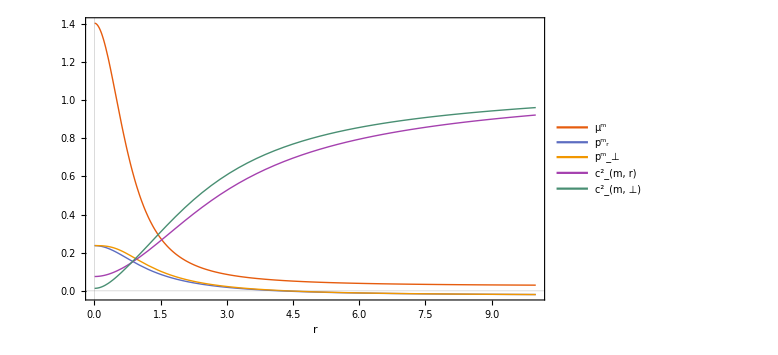

```mathematica
Plot[{μmplot/.μ1->-1.25/.ℛ->7.8/.c->0.3/.A->1.5/.α->0.001,pmrplot/.μ1->-1.25/.ℛ->7.8/.c->0.3/.A->1.5/.α->0.001,pmperpplot/.μ1->-1.25/.ℛ->7.8/.c->0.3/.A->1.5/.α->0.001,c2mr/.μ1->-1.25/.ℛ->7.8/.c->0.3/.A->1.5/.α->0.001,c2mperp/.μ1->-1.25/.ℛ->7.8/.c->0.3/.A->1.5/.α->0.001}, {r, 0.005, 10},AxesOrigin->{
0,0},PlotStyle->{Thick},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"μ^m","(p^m)_r","(p^m)_⊥","(c^2)_(m, r)","(c^2)_(m,  ⊥)"},LegendFunction->"Frame",LabelStyle->{FontSize->18, FontFamily->"Times"}],{0.9,0.35}],LabelStyle->{FontSize->18, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,""}, ImageSize->Large]
```

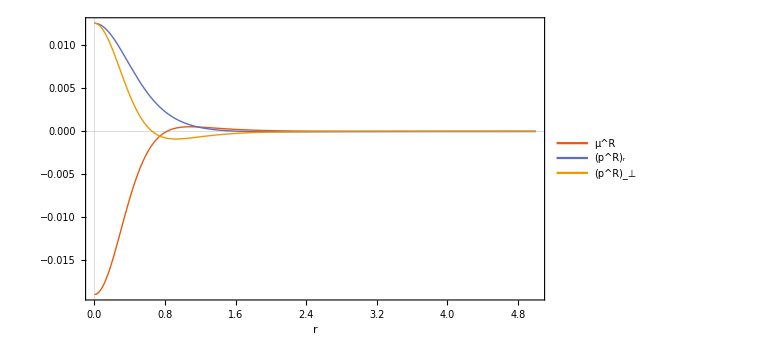

```mathematica
Plot[{μRfin/.μ1->-1.25/.ℛ->7.3/.c->0.3/.A->1.5/.α->0.001,pRrfin/.μ1->-1.25/.ℛ->7.3/.c->0.3/.A->1.5/.α->0.001,pRperpfin/.μ1->-1.25/.ℛ->7.3/.c->0.3/.A->1.5/.α->0.001}, {r, 0.001, 5},PlotRange->{0.014,-0.02},AxesOrigin->{
0,0},PlotStyle->{Thick},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"μ^R","(p^R)_r","(p^R)_⊥"},LegendFunction->"Frame",LabelStyle->{FontSize->20, FontFamily->"Times"}],{0.9,0.35}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,""}, ImageSize->Large]
```

```mathematica
Plot[{Ricci/.μ1->-1.45/.ℛ->5000/.c->0.25/.A->1.15,pmrplot/.μ1->-1.45/.ℛ->5000/.c->0.25/.A->1.15/.α->0.001,pRrfin/.μ1->-1.45/.ℛ->5000/.c->0.25/.A->1.15/.α->0.001,c2mr/.μ1->-1.45/.ℛ->5000/.c->0.25/.A->1.15/.α->0.001}, {r, 0.001, 10},AxesOrigin->{
0,0},PlotStyle->{Thick},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"R","p_(m, r)","p_(R, r)","(c_(m, r))^2"},LegendFunction->"Frame",LabelStyle->{FontSize->18, FontFamily->"Times"}],{1,0.5}],LabelStyle->{FontSize->18, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,""}, ImageSize->Large]
```

-Graphics-

```mathematica
LogPlot[{prTfin/.μ1->-1.09/.ℛ->5000/.c->0.3/.A->2.3/.α->0.001,pperpTfin/.μ1->-1.09/.ℛ->5000/.c->0.3/.A->2.3/.α->0.001,μT1/.μ1->-1.09/.ℛ->5000/.c->0.3/.A->2.3/.α->0.001}, {r, 0.01, 30},AxesOrigin->{
0,0},PlotRange->{{0.001,15},{-0.05,0.65}},PlotStyle->{Thick},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"p_r^T","(p_⊥)^T","μ^T"},LegendFunction->"Frame",LabelStyle->{FontSize->18, FontFamily->"Times"}],{1,0.5}],LabelStyle->{FontSize->18, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,""}, ImageSize->Large]
```

-Graphics-

## Plots for varied α

```mathematica
mumplot=μmplot/.μ1->-1.09/.ℛ->5000/.c->0.3/.A->2.3;
```

```mathematica
mumValpha=Plot[{mumplot/.α->0,mumplot/.α->0.001,mumplot/.α->0.01,mumplot/.α->0.03,mumplot/.α->0.04,mumplot/.α->0.05}, {r, 0.0005, 10},PlotRange->{{0,10},{-0.05,1}},AxesOrigin->{0,0},PlotStyle->{Thick},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->18, FontFamily->"Times"}],{1,0.5}],LabelStyle->{FontSize->22, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"μ_m"}, ImageSize->Large]
```

-Graphics-

```mathematica
pmrValphaplot=pmrplot/.μ1->-1.09/.ℛ->5000/.c->0.3/.A->2.3;
```

```mathematica
pmrValpha=Plot[{pmrValphaplot/.α->0,pmrValphaplot/.α->0.001,pmrValphaplot/.α->0.01,pmrValphaplot/.α->0.03,pmrValphaplot/.α->0.04,pmrValphaplot/.α->0.05}, {r, 0.0005, 10},PlotRange->{{0,10},{-0.01,0.5}},AxesOrigin->{0,0},PlotStyle->{Thick},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->18, FontFamily->"Times"}],{1,0.5}],LabelStyle->{FontSize->22, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"p_(m,  r)"}, ImageSize->Large]
```

-Graphics-

```mathematica
pmperpValphaplot=pmperpplot/.μ1->-1.09/.ℛ->5000/.c->0.3/.A->2.3;
```

```mathematica
pmperpValpha=Plot[{pmperpValphaplot/.α->0,pmperpValphaplot/.α->0.001,pmperpValphaplot/.α->0.01,pmperpValphaplot/.α->0.03,pmperpValphaplot/.α->0.04,pmperpValphaplot/.α->0.05}, {r, 0.0005, 10},PlotRange->{{0,10},{-0.01,0.5}},AxesOrigin->{0,0},PlotStyle->{Thick},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->18, FontFamily->"Times"}],{1,0.5}],LabelStyle->{FontSize->22, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"p_(⊥, r)"}, ImageSize->Large]
```

-Graphics-

```mathematica
pRrValphaplot=pRrfin/.μ1->-1.09/.ℛ->5000/.c->0.3/.A->2.3;
```

```mathematica
pRrValpha=Plot[{pRrValphaplot/.α->0,pRrValphaplot/.α->0.001,pRrValphaplot/.α->0.01,pRrValphaplot/.α->0.03,pRrValphaplot/.α->0.04,pRrValphaplot/.α->0.05}, {r, 0.0005, 10},PlotRange->{{0,10},{-0.01,0.5}},AxesOrigin->{0,0},PlotStyle->{Thick},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->18, FontFamily->"Times"}],{1,0.5}],LabelStyle->{FontSize->22, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"p_(R,  r)"}, ImageSize->Large]
```

-Graphics-

```mathematica
c2mrValphaplot=c2mr/.μ1->-1.09/.ℛ->5000/.c->0.3/.A->2.3;
```

```mathematica
c2mrValpha=Plot[{c2mrValphaplot/.α->0,c2mrValphaplot/.α->0.001,c2mrValphaplot/.α->0.01,c2mrValphaplot/.α->0.03,c2mrValphaplot/.α->0.04,c2mrValphaplot/.α->0.05}, {r, 0.005, 10},PlotRange->{{0,10},{-0.1,1}},AxesOrigin->{0,0},PlotStyle->{Thick},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->18, FontFamily->"Times"}],{1,0.5}],LabelStyle->{FontSize->22, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"(c_(m,  r))^2"}, ImageSize->Large]
```

-Graphics-

## Shell and double layer

The kinematical quantities defined on the boundary and the fluid quantities are evaluated at r_b, which is determined from the plots.

```mathematica
ϕsurface[r_,A_,ℛ_]:=(√(A^2+r^2) √(-r^2+ℛ^2))/(√(A^2+2 r^2) ℛ)
𝒜surface[r_,A_,ℛ_,μ1_,c_]:=(r^2 √(A^2+r^2) √(-r^2+ℛ^2) μ1)/(√(A^2+2 r^2) ℛ (-6+2 r^2 μ1-2 c √(3-r^2 μ1)))
Xsurf[r_,A_,ℛ_,μ1_,c_]:=-((2 r √(A^2+r^2) √(-r^2+ℛ^2) (A^6 μ1 (4 √(3-r^2 μ1) (-3+ℛ^2 μ1) (18-9 r^2 μ1+r^4 μ1^2)+c^2 √(3-r^2 μ1) (-72+15 ℛ^2 μ1-3 r^4 μ1^2-2 r^2 μ1 (-12+ℛ^2 μ1))+3 c (-3+r^2 μ1) (48-13 ℛ^2 μ1+r^4 μ1^2+2 r^2 μ1 (-6+ℛ^2 μ1)))-A^4 (-10 c^3 (-3+r^2 μ1)^3+c (-3+r^2 μ1) (32 r^6 μ1^3-18 (45+8 ℛ^2 μ1)-3 r^4 μ1^2 (71+13 ℛ^2 μ1)+18 r^2 μ1 (17+15 ℛ^2 μ1))-3 c^2 √(3-r^2 μ1) (8 r^6 μ1^3-6 (45+4 ℛ^2 μ1)-r^4 μ1^2 (71+5 ℛ^2 μ1)+2 r^2 μ1 (93+19 ℛ^2 μ1))+6 (3-r^2 μ1)^(3/2) (45+12 ℛ^2 μ1-3 r^6 μ1^3+r^4 μ1^2 (15+4 ℛ^2 μ1)-r^2 μ1 (3+26 ℛ^2 μ1)))-2 A^2 (-2 c^3 (r^2+5 ℛ^2) (-3+r^2 μ1)^3+6 (3-r^2 μ1)^(3/2) (45 ℛ^2-r^8 μ1^3+r^2 (9-39 ℛ^2 μ1)-3 r^4 μ1 (-9+ℛ^2 μ1)+r^6 μ1^2 (1+ℛ^2 μ1))+c (-3+r^2 μ1) (-810 ℛ^2+3 r^8 μ1^3+5 r^6 μ1^2 (3+ℛ^2 μ1)-3 r^4 μ1 (90+29 ℛ^2 μ1)+18 r^2 (-9+41 ℛ^2 μ1))+c^2 √(3-r^2 μ1) (810 ℛ^2+r^8 μ1^3-3 r^6 μ1^2 (1+7 ℛ^2 μ1)-18 r^2 (-9+43 ℛ^2 μ1)+3 r^4 μ1 (18+65 ℛ^2 μ1)))+4 r^2 (2 c^3 ℛ^2 (-3+r^2 μ1)^3+3 c (-3+r^2 μ1) (r^4 μ1 (48-12 r^2 μ1+r^4 μ1^2)+ℛ^2 (54-54 r^2 μ1+5 r^4 μ1^2))+2 (3-r^2 μ1)^(3/2) (6 r^4 μ1 (-6+r^2 μ1)+ℛ^2 (-27+27 r^2 μ1+3 r^4 μ1^2-r^6 μ1^3))+c^2 √(3-r^2 μ1) (-3 r^4 μ1 (24-8 r^2 μ1+r^4 μ1^2)+ℛ^2 (-162+162 r^2 μ1-39 r^4 μ1^2+4 r^6 μ1^3)))))/((A^2+2 r^2)^(7/2) ℛ^3 (3-r^2 μ1)^(3/2) (-3+r^2 μ1-c √(3-r^2 μ1))^3))
Rsurf[r_,A_,ℛ_,μ1_,c_]:= (2 (A^4 (3 c^2 (3-r^2 μ1)^(3/2)+√(3-r^2 μ1) (6 r^4 μ1^2+9 (3+ℛ^2 μ1)-2 r^2 μ1 (15+ℛ^2 μ1))+c (9 r^4 μ1^2+9 (6+ℛ^2 μ1)-2 r^2 μ1 (24+ℛ^2 μ1)))+2 r^2 (c^2 (3 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 c (6 ℛ^2-16 r^4 μ1+3 r^6 μ1^2+r^2 (18-ℛ^2 μ1))+√(3-r^2 μ1) (9 ℛ^2+6 r^6 μ1^2+3 r^2 (9+ℛ^2 μ1)-r^4 μ1 (30+ℛ^2 μ1)))+A^2 (c^2 (7 r^2+3 ℛ^2) (3-r^2 μ1)^(3/2)+c (54 ℛ^2+22 r^6 μ1^2+r^4 μ1 (-117+ℛ^2 μ1)-6 r^2 (-21+2 ℛ^2 μ1))+√(3-r^2 μ1) (27 ℛ^2+15 r^6 μ1^2-r^4 μ1 (75+2 ℛ^2 μ1)+r^2 (63+6 ℛ^2 μ1)))))/((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2)
```

```mathematica
α=0.001;
μsurface=2*α*Xsurf[r,A,ℛ,μ1,c]+(1+2*α*Rsurf[r,A,ℛ,μ1,c])*𝒜surface[r,A,ℛ,μ1,c];
psurface=(4/3)*α*Xsurf[r,A,ℛ,μ1,c]-(1/3)*(1+2*α*Rsurf[r,A,ℛ,μ1,c])*ϕsurface[r,A,ℛ];
μsurfeval=2*α*Xsurf[3.9105448,1.5,7.3,-1.25,0.3]+(1-2*α*Rsurf[3.9105448,1.5,7.3,-1.25,0.3])*(𝒜surface[3.9105448,1.5,7.3,-1.25,0.3])
psurfeval=(4/3)*α*Xsurf[3.9105448,1.5,7.3,-1.25,0.3]-(1/3)*(1-2*α*Rsurf[3.9105448,1.5,7.3,-1.25,0.3])*(ϕsurface[3.9105448,1.5,7.3])
dublayereval=-2*α*Rsurf[3.9105448,1.5,7.3,-1.25,0.3]//ScientificForm
Clear[α]
```

0.250742

-0.205695

-1.18547×10^-4

```mathematica
α=0.001;
pperpsurfeval=2*α*Xsurf[3.9105448,1.5,7.3,-1.25,0.3]-(1/2)*(1+2*α*Rsurf[3.9105448,1.5,7.3,-1.25,0.3])*ϕsurface[3.9105448,1.5,7.3]
Clear[α]
```

-0.308616

```mathematica
μS=(1+2*α*Rsurf[3.9105448,1.5,7.3,-1.25,0.3])*(𝒜surface[3.9105448,1.5,7.3,-1.25,0.3])+(2*α*Rsurf[3.9105448,1.5,7.3,-1.25,0.3])*(Xsurf[3.9105448,1.5,7.3,-1.25,0.3])
```

0.250777

```mathematica
pperpS=(2*α*Rsurf[3.9105448,1.5,7.3,-1.25,0.3])*(Xsurf[3.9105448,1.5,7.3,-1.25,0.3])-0.5*(1+2*α*Rsurf[3.9105448,1.5,7.3,-1.25,0.3])*ϕsurface[3.9105448,1.5,7.3]
```

-0.30864

```mathematica
ΠS=2*(psurfeval-pperpS)
```

0.205889

```mathematica
α=0.001;
μbarS=μS-(2*α*Rsurf[3.9105448,1.5,7.3,-1.25,0.3])*(Aschwarz+𝒜surface[3.9105448,1.5,7.3,-1.25,0.3])*Rsurf[3.9105448,1.5,7.3,-1.25,0.3]
```

0.250775

```mathematica
pperpbarS=pperpS+2*α*Rsurf[3.9105448,1.5,7.3,-1.25,0.3]*(ϕschwarz+ϕsurface[3.9105448,1.5,7.3])*Rsurf[3.9105448,1.5,7.3,-1.25,0.3]
```

-0.308631